```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
tvalue=0.4;
mub=9.27*10^(-24)*(10^19/1.6)*1000/600(**Bohr magneton=9.27*10^(-24)JT^(-1)**);
bvaluedat={0,75,150,200,300,500,600,700,900};
```

```mathematica
datrotuwsoca=Table[Flatten[Import[StringJoin["trot_",ToString[tvalue],"_nutcalca_",ToString[bvalue],"sq2.dat"]]],{bvalue,bvaluedat}];
datrotdwsoca=Table[Flatten[Import[StringJoin["trot_",ToString[tvalue],"_ndtcalca_",ToString[bvalue],"sq2.dat"]]],{bvalue,bvaluedat}];
datrotuwsocb=Table[Flatten[Import[StringJoin["trot_",ToString[tvalue],"_nutcalcb_",ToString[bvalue],"sq2.dat"]]],{bvalue,bvaluedat}];
datrotdwsocb=Table[Flatten[Import[StringJoin["trot_",ToString[tvalue],"_ndtcalcb_",ToString[bvalue],"sq2.dat"]]],{bvalue,bvaluedat}];
```

```mathematica
momentax=Table[Total[Flatten[ Import[StringJoin["trot_",ToString[tvalue],"_allmtax_",ToString[bvalue],"sq2.dat"]][[1]][[{1,5,9}]]]],{bvalue,bvaluedat}];
momentbx=Table[Total[Flatten[ Import[StringJoin["trot_",ToString[tvalue],"_allmtbx_",ToString[bvalue],"sq2.dat"]][[1]][[{1,5,9}]]]],{bvalue,bvaluedat}];


mgdata=Table[{bvaluedat[[i]]*Sqrt[2]*mub/0.5,((momentax+momentbx)/2)[[i]]},{i,1,Length[bvaluedat]}];

diffmgdata = Table[{bvaluedat[[i]]*Sqrt[2]*mub/0.5,((momentbx-momentax))[[i]]},{i,1,Length[bvaluedat]}];
```

```mathematica
occupationa=Table[Table[Partition[(datrotuwsoca[[l]]+datrotdwsoca[[l]]),3][[i,1]] + Partition[(datrotuwsoca[[l]]+datrotdwsoca[[l]]),3][[i,2]]+ Partition[(datrotuwsoca[[l]]+datrotdwsoca[[l]]),3][[i,3]],{i,1,Nx*Ny}][[1]],{l,1,Length[bvaluedat]}];


occupationb=Table[Table[Partition[(datrotuwsocb[[l]]+datrotdwsocb[[l]]),3][[i,1]] + Partition[(datrotuwsocb[[l]]+datrotdwsocb[[l]]),3][[i,2]]+ Partition[(datrotuwsocb[[l]]+datrotdwsocb[[l]]),3][[i,3]],{i,1,Nx*Ny}][[1]],{l,1,Length[bvaluedat]}];
Table[{bvaluedat[[i]]*Sqrt[2]*mub/0.5,(occupationb-occupationa)[[i]]},{i,1,Length[bvaluedat]}];
Table[{bvaluedat[[i]]*Sqrt[2]*mub/0.5,((occupationb+occupationa)/2)[[i]]},{i,1,Length[bvaluedat]}];
```

```mathematica
occudata=Take[Table[{bvaluedat[[i]]*Sqrt[2]*mub/0.5,(occupationb-occupationa)[[i]]},{i,1,Length[bvaluedat]}],(Length[bvaluedat])];
```

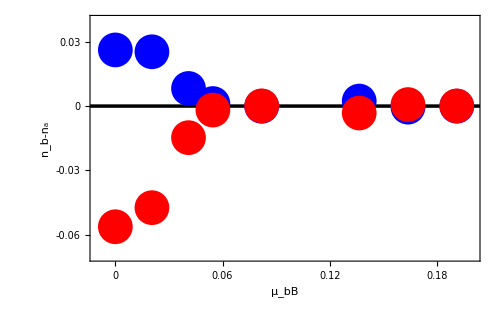

```mathematica
crossingpt=0;
occuplot=ListPlot[{diffmgdata,occudata},Frame->True,FrameStyle->Directive[Thickness[0.005],Black,32],Epilog->{{Blue,PointSize[0.05],Point[occudata]},{Red,PointSize[0.05],Point[diffmgdata]}},
GridLines->{None,{0}},GridLinesStyle->Directive[Black, Thickness[0.005]],PlotRange->{{-0.01,0.2},{-0.07,0.04}},
FrameTicks->{{{{-0.06,-0.06,0.03},{-0.03,-0.03,0.03},{0,0,0.03},{0.03,0.03,0.03}},{{-0.06,Null,0.03},{-0.03,Null,0.03},{0,Null,0.03},{0.03,Null,0.03}}},{{{0,0,0.03},{0.06,0.06,0.03},{0.12,0.12,0.03},{0.18,0.18,0.03},{0.24,0.24,0.03}},{{0,Null,0.03},{0.06,Null,0.03},{0.12,Null,0.03},{0.18,Null,0.03},{0.24,Null,0.03}}}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,25]},
FrameLabel->{{Style["n_b-n_a",35,Blue,FontFamily->"TimesNewRoman"],Style["M_tb-M_ta",35,Red,FontFamily->"TimesNewRoman"]},{Style["μ_bB",35,FontFamily->"TimesNewRoman"],None}},ImagePadding->{{125,45},{90,17}},ImageSize->500]
Export["occuandmgplot.eps",occuplot];
```